# Anharmonic Oscillator T=0

## Functions

Implements the Recursion Relation for the Anharmonic Oscillator with Hamiltonian . The recursion relation is and it's valid for .

```mathematica
reqRel[t_]:=EE*(t-3)*ToExpression["x"<>ToString[t-4]]+1/4*(t-4)*(t-5)*(t-3)*ToExpression["x"<>ToString[t-6]]-(t-1)*ToExpression["x"<>ToString[t]]-(t-2)*gg*ToExpression["x"<>ToString[t-2]]==0;
```

Generates the Hankel Matrix at depth k with recursion relation as defined in above. Used in every case.

```mathematica
buildMatrix[k_Integer]:=Function[{e,g,x2},Module[{rels,rules,xi,sol,mat},
(*Generate relation equations*)rels=Table[reqRel[2 j],{j,2,k+1}];

(*Build rules step by step*)rules={};
Do[If[i>0,xi=ToExpression["x"<>ToString[2 i+2]];
sol=First[Solve[rels[[i]]/. rules,xi]];
rules=FullSimplify[Join[rules,sol]],
(*else base case:i==0*)
rules={ToExpression["x0"]->1}],{i,0,k}];
(*Build the matrix*)
mat=Table[If[OddQ[i+j],0,If[i==0&&j==0,1,ToExpression["x"<>ToString[i+j]]]],{i,0,k},{j,0,k}];
(*Substitute rules and parameters*)
mat/. rules/. {EE->e,gg->g,ToExpression["x"<>ToString[2]]->x2}]];
```

Retrieves only the allowed energies. Returns an array of arrays of the form: {{e1,tstar1,x2star1},{e2,tstart2,x2star2}...}

```mathematica
allowedEnergies[list_]:=Module[{acceptedValues={}},
Do[
If[values[[2]]>=0,
acceptedValues=Join[acceptedValues,{{values[[1]],values[[2]],values[[3]],values[[4]],1}}];,
acceptedValues=Join[acceptedValues,{{values[[1]],values[[2]],values[[3]],values[[4]],0}}]
]
,{values,list}];
acceptedValues
]
```

Takes a search space[two item list], a step[float], a depth(k)[integer], a coupling(g)[float],  method[string] with the default value being mathematica and a tolerance[float] with the default value being 10⁻⁸. Builds a hankel matrix with the depth, does the sdp with the desired method, finds the allowed energies in the search space and returns a list of lists for the allowed values and a dictionary of dictionaries for the full data.

```mathematica
doSDPAtK[searchspace_,step_,g_,k_,tolerance_:10^(-8)]:=Module[
{
(*Initiates Matt as the Hankel Matrix at depth K
matt[e]-tI>=0
*)
matt=buildMatrix[k],
(*Initiates Containers*)
allowedDataAtK,fullDataAtK={},
(*Initiates several other internal variables*)
constraintMatrixConstant,constraintMatrixCoefficient,t,tstar,x2star,eigenvalue,xVec,numericM
},
Do[
constraintMatrixConstant:=FullSimplify[matt[e,g,0]];
constraintMatrixCoefficient=Coefficient[FullSimplify[matt[e,g,x2]],x2];
xVec=SemidefiniteOptimization[
-t,{VectorGreaterEqual[{constraintMatrixConstant+x2*constraintMatrixCoefficient,t IdentityMatrix[k+1]},{"SemidefiniteCone", k+1}]},
{t,x2},{"PrimalMinimizerVector"},Method->"MOSEK",Tolerance->tolerance
];
If[!VectorQ[xVec[[1]],NumericQ],Print["Non-numeric solution at e = ",e];];
{tstar,x2star}={xVec[[1]][[1]],xVec[[1]][[2]]};
numericM=FullSimplify[N[matt[e,g,x2star]]];
eigenvalue=Min[Eigenvalues[FullSimplify[numericM]]];
fullDataAtK=Join[fullDataAtK,{{e,tstar,eigenvalue,x2star}}];
,{e,searchspace[[1]],searchspace[[-1]],step}];
allowedDataAtK=allowedEnergies[fullDataAtK];
allowedDataAtK
]
```

## Code Execution

Define an Energy Search Space with a step and the Coupling g

```mathematica
eRange={0,5};
eStep=0.1;
g=-5
```

Collect Data

```mathematica
data=<||>;
```

```mathematica
Do[
data[k]=doSDPAtK[eRange,eStep,g,k]
,{k,4,10,1}]
```

Plot as desired

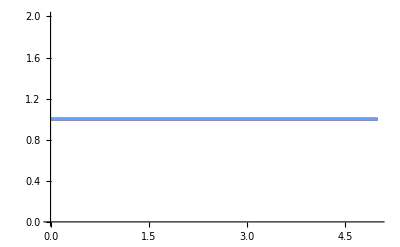

```mathematica
ListPlot[Table[Transpose[{#[[1]]&/@data[k],#[[-1]]&/@data[k]}],{k,4,10,1}],Joined->True,PlotLegends->Placed[LineLegend[Automatic,"K = "<>ToString/@Range[10,10,2]],Right]]
```

Make an area plot manually to compare

```mathematica
list=ListPlot[Table[Transpose[{#[[1]]&/@data[k],#[[4]]&/@data[k]}],{k,7,7,2}],Joined->True];
```

```mathematica
region=RegionPlot[Min[Eigenvalues[buildMatrix[7][e,-5,xx2]]]>=0,{e,eRange[[1]],eRange[[2]]},{xx2,0,2},PlotStyle->LightBlue,BoundaryStyle->Black];
```

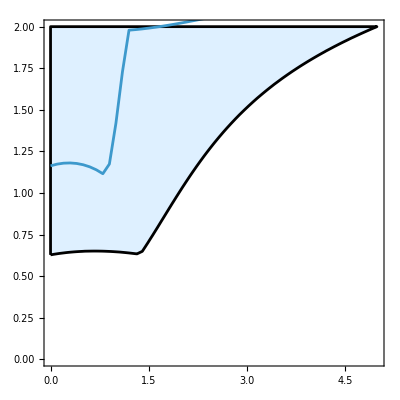

```mathematica
Show[region,list]
```